# Ising Model Simulation

## Definitions

```mathematica
(*Argumentative function to handle periodic boundary conditions*)pbc[z_,size_]:=If[z>size,z-size,If[z<1,z+size,z]]

(*pointenergy of sx,sy is determined by the sum of nearest neighbors' ising values x ising of sx,sy*)

pointenergy[sx_,sy_]:=Module[{neighbors},neighbors={
ising[[pbc[sx-1,size]]][[sy]],
ising[[pbc[sx+1,size]]][[sy]],
ising[[sx]][[pbc[sy-1,size]]],
ising[[sx]][[pbc[sy+1,size]]]};
-Total[neighbors]*ising[[sx,sy]]]

(*Total energy is the sum of the point energies over the whole array / 2*)
totalenergy :=Sum[Sum[pointenergy[i,j],{i,1,size}],{j,1,size}]/2

(*Flip if -2(energy level of sx, sy) is negative, or we add a noise layer according to the boltz const*)
flip:=Module[{sx,sy,ediff,sdiff,p},
{sx,sy}=RandomInteger[{1,size},2];ediff=-2*pointenergy[sx,sy];sdiff=-2*ising[[sx]][[sy]];boltz=Exp[-ediff/temperature];If[ediff<=0||RandomReal[]<boltz,ising[[sx]][[sy]]*=-1;energy+=ediff;spin+=sdiff;
]]
```

## Initializations

```mathematica
(*Global Variables*)
size=100;
ising=RandomChoice[{-1,1},{size,size}]; (*size by size array*)

(*define set delayed variables for spin, energy, and plots*)
spin:=totalspin;
energy:=totalenergy;
arrayPlot:=ArrayPlot[ising,PlotRange->{-1,1},Mesh->True];
totalspin:=Total[Flatten[ising]];
```

```mathematica
Dynamic[arrayPlot]
```

```mathematica
Dynamic[flipcount]
Dynamic[N[temperature]]
Dynamic[spin]
Dynamic[energy]
```

## Simulation

```mathematica
(*Define global variables for simulation*)
J=+1;
movenum=5*10^5;
temperature = 6;
flipcount=0;

flushnum=Min[10^4,movenum/100];
keepnum=movenum/flushnum;
deltaT=-temperature/movenum;

(*Clearing cache lists*)
flushlist={};
keeplist={};

(*Simulation loop*)
Do[flip;
flipcount++;
temperature+=deltaT;
AppendTo[flushlist,{temperature, spin, energy, energy^2}];
If[Mod[flipcount,flushnum]==0,
AppendTo[keeplist,Mean[flushlist]];
flushlist={};
ClearSystemCache[];
];
Pause[0.0],{movenum}]
```

## Analysis

```mathematica
(*Variables to graph*)
```

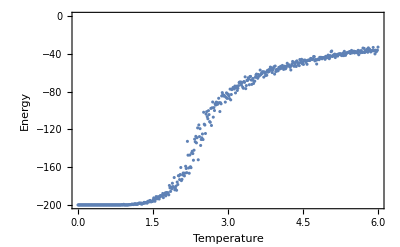

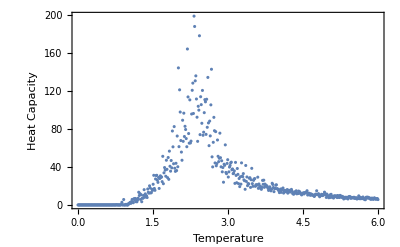

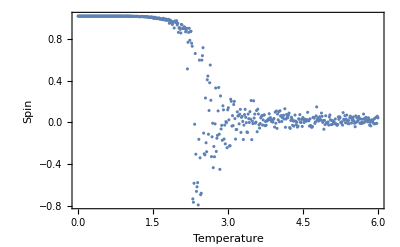

```mathematica
{tlist,slist, elist, elist2}=Transpose[keeplist];
hlist = (elist2-elist^2)/tlist^2;

(*plotting*)
ListPlot[Transpose[{tlist, elist}], PlotRange->All, BaseStyle->{FontSize->18}, AxesOrigin->{2.269,0},Frame->True, FrameLabel->{"Temperature", "Energy"}]

ListPlot[Transpose[{tlist, hlist}], PlotRange->All, BaseStyle->{FontSize->18}, AxesOrigin->{2.269,0},Frame->True, FrameLabel->{"Temperature", "Heat Capacity"}]

spinplot =ListPlot[Transpose[{tlist, slist/(size^2)}], PlotRange->All, BaseStyle->{FontSize->18}, AxesOrigin->{2.269,0},Frame->True, FrameLabel->{"Temperature", "Spin"}]
```

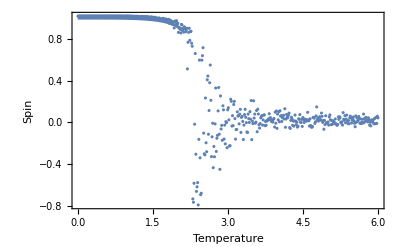

```mathematica
Tc=2.269;
onsanger = (1-(Sinh[Log[(1+2^(1/2))*(Tc/T)]])^(-4))^(1/8);
onsplot = Plot[onsanger,{T,0,Tc}];
Show[spinplot,onsplot]
```

## Theory Questions

#### Transition temperature (𝑇𝑐) observed vs. transition temperature predicted by mean - field - theory vs transition temperature form Onsager' s exact calculation

My observed Transition Temperature (𝑇𝑐) is about the same as the Onsager calculation, as you can see above. However Onsager’s Exact Calculation is an exact calculation, while mine is a bit more noisy. Contrastingly, the Mean-Field Theory prediction overestimates transition temperature to be about 6 K due to neglecting spatial correlations.

#### Why does the average spin doesn’t rise abruptly from zero at the transition, but instead appears to fluctuate wildly just above the transition?

So the average spin is not an abrupt transition because it is a continuous phase transition, and as the random changes are possible  just above phase transitions, any point in energy could flip and then everything around changes since the energy levels are determined by the nearest neighbors.

#### Why is this proven by critical opalescence?

So critical opalescence is when there is an increase in scattered light near the critical point of a phase transition, and we can observe the scattered light.  It scatters because the wavelength of light is about the size of the “correlation length”, and so the light waves are scattered. And thus opalescence proves that the divergence of critical density fluctuations to macroscopic length scales near the phase transition